-Graphics3D-

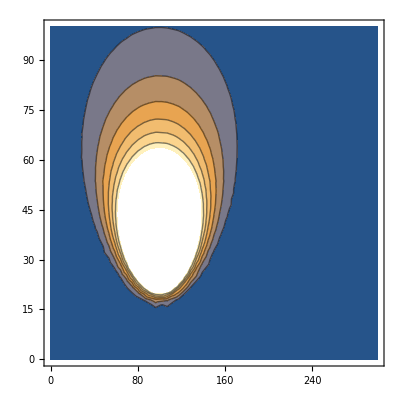

```mathematica
vData = {100,150,50};
pPrior[μ_,σ_] := 1/(σ^2);
pLikelihood[μ_,σ_]:= Likelihood[NormalDistribution[μ,σ],vData];
pPosteriorNumerator[μ_,σ_]:= pPrior[μ,σ] * pLikelihood[μ,σ];
Plot3D[pPosteriorNumerator[μ,σ],{μ,0,300},{σ,0,100},PlotRange->Full]
ContourPlot[pPosteriorNumerator[μ,σ],{μ,0,300},{σ,0,100}]
Integrate[1/(σ^2)*Likelihood[NormalDistribution[μ,σ],vData],{μ,0,300}]
```

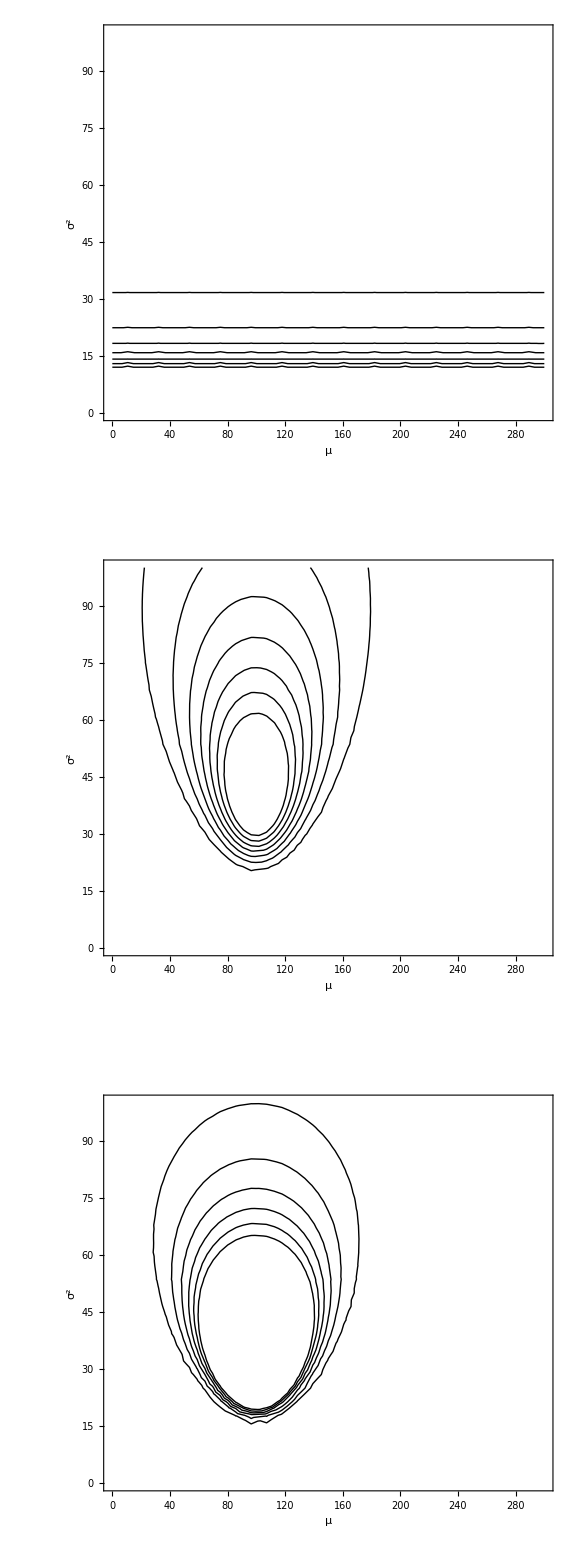

```mathematica
g1 = ContourPlot[pPrior[μ,σ],{μ,0,300},{σ,0,100},ContourShading->{White},ContourStyle->{Black},FrameLabel->{μ,σ^2}];
g2 = ContourPlot[pLikelihood[μ,σ],{μ,0,300},{σ,0,100},ContourShading->{White},ContourStyle->{Black},FrameLabel->{μ,σ^2}];
g3 = ContourPlot[pPosteriorNumerator[μ,σ],{μ,0,300},{σ,0,100},ContourShading->{White},ContourStyle->{Black},FrameLabel->{μ,σ^2}];
Show[GraphicsColumn[{g1,g2,g3}],ImageSize->Large]
```

```mathematica
pPosteriorMarginalMu[μ_]= Integrate[pPosteriorNumerator[μ,σ],{σ,0,∞}]
```

ConditionalExpression[1/(√2 π^(3/2) (35000-600 μ+3 μ^2)^2),Re[(-200+μ) μ]>-35000/3]

```mathematica
pPosteriorMarginalMuSimple[μ_]:=1/(√2 π^(3/2) (35000-600 μ+3 μ^2)^2)
```

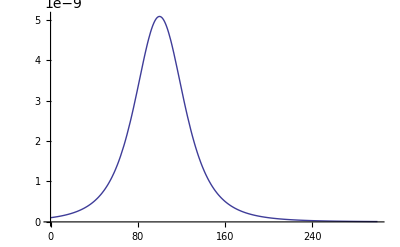

```mathematica
Rotate[Plot[pPosteriorMarginalMuSimple[μ],{μ,0,300}],π/2]
```

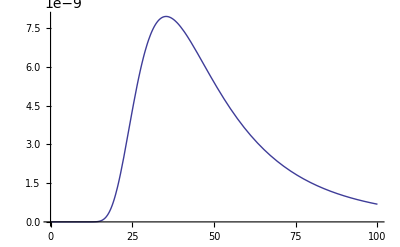

```mathematica
pPosteriorMarginalSigma[σ_]= Integrate[pPosteriorNumerator[μ,σ],{μ,0,300}];
Plot[pPosteriorMarginalSigma[σ],{σ,0,100}]
```

## Now doing the marginals properly using the analytic results

```mathematica
pPosteriorMarginalMuCorrect[μ_]:=PDF[StudentTDistribution[Mean[vData],Sqrt[Variance[vData]/Length[vData]],Length[vData]-1],{μ}]
```

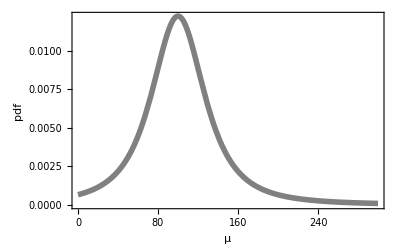

```mathematica
gPosteriorMarginalMu=Plot[pPosteriorMarginalMuCorrect[μ],{μ,0,300},FrameLabel->{μ,pdf},Frame->{True,True,False,False},BaseStyle->{FontSize->16},PlotStyle->{Thickness[0.01],Gray}]
```

```mathematica
pPosteriorMarginalSigmaCorrect[σ_]:=PDF[InverseChiSquareDistribution[Length[vData]-1,Sqrt[Variance[vData]/Length[vData]]],{σ}]
```

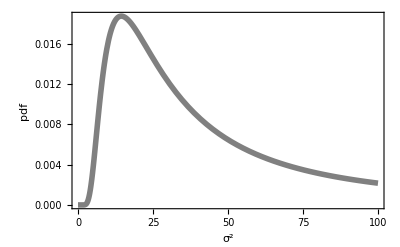

```mathematica
gPosteriorMarginalSigma=Rotate[Plot[pPosteriorMarginalSigmaCorrect[σ],{σ,0,100},FrameLabel->{σ^2,pdf},Frame->{True,True,False,False},BaseStyle->{FontSize->16},PlotStyle->{Thickness[0.01],Gray}],π/2]
```

```mathematica
pPriorSigma[σ_]:=pPrior[10,σ]
```

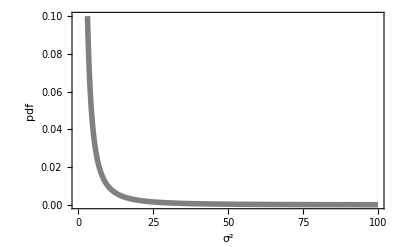

```mathematica
gPriorMarginalMu=Rotate[Plot[pPriorSigma[σ],{σ,0,100},PlotRange->{{0,100},{0,0.1}},FrameLabel->{σ^2,pdf},Frame->{True,True,False,False},BaseStyle->{FontSize->16},PlotStyle->{Thickness[0.01],Gray}],π/2]
```

```mathematica
GraphicsGrid[{{g1,gPriorMarginalMu},{g2,},{g3,gPosteriorMarginalSigma},{gPosteriorMarginalMu,}}]
```

-Graphics-

## Idealised example for Stack Exchange

```mathematica
ClearAll["Global`*"]
```

```mathematica
vData = {100,150,50};
pPrior[μ_,σ_] := 1/(σ^2);
pLikelihood[μ_,σ_]:= Likelihood[NormalDistribution[μ,σ],vData];
pPosteriorNumerator[μ_,σ_]:= pPrior[μ,σ] * pLikelihood[μ,σ];
g3 = ContourPlot[pPosteriorNumerator[μ,σ],{μ,0,300},{σ,0,100},ContourShading->{White},ContourStyle->{Black},FrameLabel->{μ,σ^2},BaseStyle->{FontSize->16}];
pPriorSigma[σ_]:=pPrior[10,σ]
pPosteriorMarginalSigmaCorrect[σ_]:=PDF[InverseChiSquareDistribution[Length[vData]-1,Sqrt[Variance[vData]/Length[vData]]],{σ}]
gPosteriorMarginalSigma=Rotate[Plot[pPosteriorMarginalSigmaCorrect[σ],{σ,0,100},FrameLabel->{σ^2,pdf},Frame->{True,True,False,False},BaseStyle->{FontSize->16},PlotStyle->{Thickness[0.01],Gray}],π/2];
pPosteriorMarginalMuCorrect[μ_]:=PDF[StudentTDistribution[Mean[vData],Sqrt[Variance[vData]/Length[vData]],Length[vData]-1],{μ}]
gPosteriorMarginalMu=Plot[pPosteriorMarginalMuCorrect[μ],{μ,0,300},FrameLabel->{μ,pdf},Frame->{True,True,False,False},BaseStyle->{FontSize->16},PlotStyle->{Thickness[0.01],Gray}];
GraphicsGrid[{{g3,gPosteriorMarginalSigma},{gPosteriorMarginalMu,}}]
```

-Graphics-

```mathematica
vData={100,150,50};
pPrior[μ_,σ_]:=1/(σ^2);
pLikelihood[μ_,σ_]:=Likelihood[NormalDistribution[μ,σ],vData];
pPosteriorNumerator[μ_,σ_]:=pPrior[μ,σ]*pLikelihood[μ,σ];
g3=ContourPlot[pPosteriorNumerator[μ,σ],{μ,0,300},{σ,0,100},ContourShading->{White},ContourStyle->{Black},FrameLabel->{μ,σ^2},BaseStyle->{FontSize->16}];
pPriorSigma[σ_]:=pPrior[10,σ]
pPosteriorMarginalSigmaCorrect[σ_]:=PDF[InverseChiSquareDistribution[Length[vData]-1,Sqrt[Variance[vData]/Length[vData]]],{σ}]
gPosteriorMarginalSigma=Rotate[Plot[pPosteriorMarginalSigmaCorrect[σ],{σ,0,100},FrameLabel->{σ^2,pdf},Frame->{True,True,False,False},BaseStyle->{FontSize->16},PlotStyle->{Thickness[0.01],Gray}],π/2];
pPosteriorMarginalMuCorrect[μ_]:=PDF[StudentTDistribution[Mean[vData],Sqrt[Variance[vData]/Length[vData]],Length[vData]-1],{μ}]
gPosteriorMarginalMu=Plot[pPosteriorMarginalMuCorrect[μ],{μ,0,300},FrameLabel->{μ,pdf},Frame->{True,True,False,False},BaseStyle->{FontSize->16},PlotStyle->{Thickness[0.01],Gray}];
GraphicsGrid[{{g3,gPosteriorMarginalSigma},{gPosteriorMarginalMu,}}]
```

-Graphics-

## Doing the 3D plots

```mathematica
ViewPoint1={-2.7553442555157543,-0.01528734644048391,1.9641395904148917};
ViewVertical1={0.,0.,1.};
h1=Plot3D[pPrior[μ,σ],{μ,0,300},{σ,0,100},AxesLabel->{μ,σ^2,pdf   },BaseStyle->{FontSize->16},Boxed->False,ColorFunction->"GrayTones",Ticks->{All,All,None},PlotRange->{Automatic,Automatic,{0,0.1}},ViewPoint->ViewPoint1,ViewVertical->ViewVertical1];
h2=Plot3D[pLikelihood[μ,σ],{μ,0,300},{σ,0,100},AxesLabel->{μ,σ^2,likelihood},BaseStyle->{FontSize->16},Boxed->False,ColorFunction->"GrayTones",PlotRange->{Automatic,Automatic,Full},ViewPoint->ViewPoint1,ViewVertical->ViewVertical1,Ticks->{All,All,None}];
h3 = Plot3D[pPosteriorNumerator[μ,σ],{μ,0,300},{σ,0,100},AxesLabel->{μ,σ^2,pdf},BaseStyle->{FontSize->16},Boxed->False,ColorFunction->"GrayTones",PlotRange->{Automatic,Automatic,Full},ViewPoint->ViewPoint1,ViewVertical->ViewVertical1,Ticks->{All,All,None}];
GraphicsColumn[{h1,h2,h3}]
```

-Graphics-